```mathematica
ClearAll["Global`*"]; 

(*Now define the function fresh*)
threeBodyBifurcation[seed_,ymin_,ymax_,tmax_:100,stepSize_:0.02,nSamples_:50]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,bifurcationData={},filteredData={},q2xValues,currentQ2x,x1val,tSample,count=0},(*Set the random seed*)SeedRandom[seed];
(*Fixed initial conditions*)q2y=RandomReal[{0,10}];
q3x=RandomReal[{-10,0}];
q3y=RandomReal[{5,20}];
Print["Fixed initial conditions (seed = ",seed,"):"];
Print["q2y = ",q2y];
Print["q3x = ",q3x];
Print["q3y = ",q3y];
Print["y-axis range: [",ymin,", ",ymax,"]"];
Print["Step size: ",stepSize];
Print["Samples per q2x: ",nSamples];
(*Generate q2x values*)q2xValues=Range[5,20,stepSize];
Print["Running ",Length[q2xValues]," simulations..."];
(*Run simulations*)Do[count++;
If[Mod[count,50]==0,Print["Progress: ",count,"/",Length[q2xValues]]];
(*Set initial conditions*)pos1={0,0};
vel1={0,10}*conv;
pos2={currentQ2x,q2y};
vel2={-10,0}*conv;
pos3={q3x,q3y};
vel3={0,0};

(*Solve ODE*)sol=Quiet@Check[NDSolve[{x1''[t]==G m2 (x2[t]-x1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2)+G m3 (x3[t]-x1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^(3/2),y1''[t]==G m2 (y2[t]-y1[t])/((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(3/2)+G m3 (y3[t]-y1[t])/((x3[t]-x1[t])^2+(y3[t]-y1[t])^2)^(3/2),x2''[t]==G m1 (x1[t]-x2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2)+G m3 (x3[t]-x2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^(3/2),y2''[t]==G m1 (y1[t]-y2[t])/((x1[t]-x2[t])^2+(y1[t]-y2[t])^2)^(3/2)+G m3 (y3[t]-y2[t])/((x3[t]-x2[t])^2+(y3[t]-y2[t])^2)^(3/2),x3''[t]==G m1 (x1[t]-x3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)+G m2 (x2[t]-x3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2),y3''[t]==G m1 (y1[t]-y3[t])/((x1[t]-x3[t])^2+(y1[t]-y3[t])^2)^(3/2)+G m2 (y2[t]-y3[t])/((x2[t]-x3[t])^2+(y2[t]-y3[t])^2)^(3/2),(*Initial conditions*)x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]},{x1,y1,x2,y2,x3,y3},{t,0,tmax},MaxSteps->50000,Method->"StiffnessSwitching"],$Failed];
If[sol=!=$Failed,(*Sample at random times in the last 20% of simulation*)Do[tSample=RandomReal[{0.8*tmax,tmax}];
x1val=Evaluate[x1[tSample]/. sol[[1]]];
(*Only keep points within our y-range*)If[ymin<=x1val<=ymax,AppendTo[bifurcationData,{currentQ2x,x1val}];];,{nSamples}];],{currentQ2x,q2xValues}];

Print["\nTotal points within y-range: ",Length[bifurcationData]];
(*Filter data to ensure all points are within range*)filteredData=Select[bifurcationData,ymin<=#[[2]]<=ymax&];
(*Create and return the plot*)ListPlot[filteredData,PlotStyle->{PointSize[0.001]},(*Small dots*)Joined->False,AxesLabel->{"X_2(initial position)","X_1 at late times"},ImageSize->Large,PlotLabel->Row[{"Bifurcation Diagram - Three Body Problem\nSeed = ",seed}],ImageSize->800,PlotRange->{{5,20},{ymin,ymax}},GridLines->Automatic]]
```

Fixed initial conditions (seed = 12):

q2y = 1.40802

q3x = -9.63556

q3y = 12.8212

y-axis range: [-100, 100]

Step size: 0.02

Samples per q2x: 50

Running 751 simulations...

Progress: 50/751

Progress: 100/751

Progress: 150/751

Progress: 200/751

Progress: 250/751

Progress: 300/751

Progress: 350/751

Progress: 400/751

Progress: 450/751

Progress: 500/751

Progress: 550/751

Progress: 600/751

Progress: 650/751

Progress: 700/751

Progress: 750/751

Total points within y-range: 36280

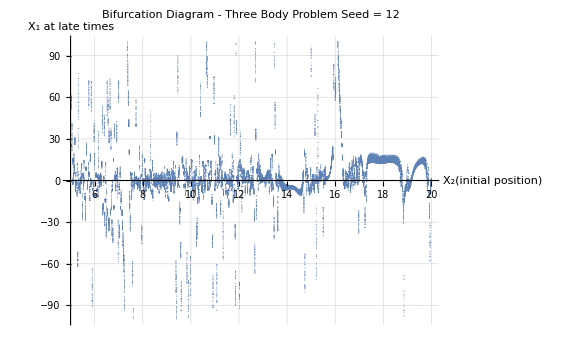

Fixed initial conditions (seed = 67):

q2y = 0.41334

q3x = -7.08008

q3y = 16.8764

y-axis range: [-100, 100]

Step size: 0.02

Samples per q2x: 50

Running 751 simulations...

Progress: 50/751

Progress: 100/751

Progress: 150/751

Progress: 200/751

Progress: 250/751

Progress: 300/751

Progress: 350/751

Progress: 400/751

Progress: 450/751

Progress: 500/751

Progress: 550/751

Progress: 600/751

Progress: 650/751

Progress: 700/751

Progress: 750/751

Total points within y-range: 35495

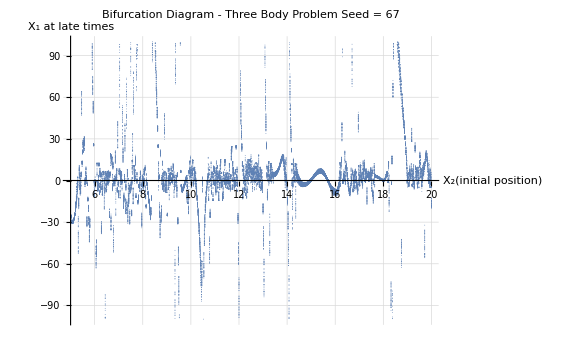

```mathematica
(*Test with different seed*)
threeBodyBifurcation[12,-100,100]

(*Narrower y-range*)
threeBodyBifurcation[67,-100,100]
```